# Crank-Nicholson Method

```mathematica
Clear["`*"];
```

## Essential Modules and Setup

### Defining Coefficients

```mathematica
Clear[coeffP12,coeffP6,coeffP8,coeffT4,coeffT6,coeffP10,coeffT8,coeffT42D,centeredExplicitScheme,coeffNJT82D,coeffNJP62D,coeffNJP82D];

coeffVariables={
α,β,
α12,β12,
α21,α22,β22,
β31,α31,α32,β32,
β41,α41,α42,β42,
a,b,c,d,
a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,
a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,
a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,
a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4
};
coeffAllZero={
α->0,β->0,
α12->0,β12->0,
α21->0,α22->0,β22->0,
β31->0,α31->0,α32->0,β32->0,
β41->0,α41->0,α42->0,β42->0,
a->0,b->0,c->0,d->0,
a1->0,b1->0,c1->0,d1->0,e1->0,f1->0,g1->0,h1->0,i1->0,j1->0,k1->0,
a2->0,b2->0,c2->0,d2->0,e2->0,f2->0,g2->0,h2->0,i2->0,j2->0,k2->0,
a3->0,b3->0,c3->0,d3->0,e3->0,f3->0,g3->0,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

centeredExplicitScheme=Join[{
a->1
},coeffAllZero
];

coeffNJP82D=Join[{a->320/393,b->310/393,α->344/1179,β->23/2358,a1->2186893/101340,b1->526369/5067,c1->-3296517/11260,d1->1940803/10134,e1->-583529/20268,f1->14802/2815,g1->-14839/20268,h1->2659/50670,a2->17692549/26588340,b2->76400497/26588340,c2->-22430799/2954260,d2->20890601/5317668,e2->502259/5317668,f2->109179/2954260,g2->-175997/26588340,h2->13231/26588340,α12->18922/563,β12->65943/563,α21->4765/147713,α22->505611/147713,β22->86431/147713},coeffAllZero];

coeffNJP62D=Join[{a->120/97,α->12/97,β->-1/194,a1->177/16,b1->-507/8,c1->783/8,d1->-201/4,e1->81/16,f1->-3/8,α12->11/2,β12->-131/4},coeffAllZero];

coeffNJT82D=Join[{a->147/152,b->51/95,a3->-23/760,α->9/38,a1->16530161/1123920,b1->-1906382/70245,c1->12157/2230,d1->154559/10035,e1->-223439/16056,f1->8648/1115,g1->-56333/20070,h1->42397/70245,i1->-7327/124880,a2->50985901/76680576,b2->8460292/2995335,c2->-14091773/1711620,d2->9343009/1711620,e2->-4738699/5477184,f2->30475/171162,g2->-53789/1711620,h2->45511/11981340,i2->-86431/383402880,a3->-86431/2051280,b3->153773/512820,c3->523003/73260,d3->-235109/14652,e3->289571/29304,f3->-106703/73260,g3->18761/73260,h3->-17461/512820,i3->953/410256,α12->3044/223,α21->2437/76072,α22->125603/38036,α31->-29/407,α32->2437/407},coeffAllZero];

coeffNJP8=Join[{a->40/27,b->25/54,α->4/9,β->1/36,a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,a2->-257/1080,b2->-107/60,c2->-5/24,d2->55/27,e2->5/24,f2->-1/60,g2->1/1080,a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,a4->-1/600,b4->-101/600,c4->-17/24,d4->0,e4->17/24,f4->101/600,g4->1/600,α12->12,β12->15,α21->1/18,α22->5/2,β22->10/9,β31->1/90,α31->4/15,α32->8/9,β32->1/6,β41->1/20,α41->1/2,α42->1/2,β42->1/20},coeffAllZero];

coeffT4=Join[{α->1/4,α12->3,a->3/2,a1->-17/6,b1->3/2,c1->3/2,d1->-1/6},coeffAllZero];

coeffT42D=Join[{α->1/10,α12->10,a->6/5,a1->145/12,b1->-76/3,c1->29/2,d1->-4/3,e1->1/12},coeffAllZero];

coeffNJT62D=Join[{a->12/11,b->3/11,α->2/11,a1->13097/990,b1->-2943/110,c1->573/44,d1->167/99,e1->-18/11,f1->57/110,g1->-131/1980,a2->48241/110160,b2->1821/340,c2->-10453/816,d2->1283/162,e2->-281/272,f2->143/1020,g2->-1169/110160,α12->126/11,α21->5/612,α22->339/68},coeffAllZero];

coeffT6=Join[{
α->1/3,
α12->5,
α21->1/8,α22->3/4,
a->14/9,b->1/9,c->0,d->0,
a1->-197/60,b1->-5/12,c1->5,d1->-5/3,e1->5/12,f1->-1/20,
a2->-43/96,b2->-5/6,c2->9/8,d2->1/6,e2->-1/96
},coeffAllZero];

coeffT8=Join[{
α->3/8,
α12->7,
α21->1/12,α22->5/4,
α31->13/55,α32->6/11,
a->25/16,b->1/5,c->-1/80,
a1->-503/140,b1->-63/20,c1->21/2,d1->-35/6,e1->35/12,f1->-21/20,g1->7/30,h1->-1/42,
a2->-79/240,b2->-77/60,c2->55/48,d2->5/9,e2->-5/48,f2->1/60,g2->-1/720,
a3->-1/66,b3->-2051/3300,c3->-53/132,d3->31/33,e3->7/66,f3->-1/132,g3->1/3300
},coeffAllZero];


coeffP6=Join[{
α->17/57,β->-1/114,
α12->8,β12->6,
a->30/19,b->0,c->0,d->0,
a1->-43/12,b1->-20/3,c1->9,d1->4/3,e1->-1/12
},coeffAllZero];

coeffP8=Join[{
α->4/9,β->1/36,
α12->12,β12->15,
α21->2,α22->2/3,β22->1/15,
a->40/27,b->25/54,
a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,
a2->-247/900,b2->-19/12,c2->1/3,d2->13/9,e2->1/12,f2->-1/300
},coeffAllZero];

coeffP10={
α->1/2,β->1/20,
α12->16,β12->28,
α21->1/21,α22->3,β22->5/3,
β31->1/90,α31->4/15,α32->8/9,β32->1,
β41->0,α41->0,α42->0,β42->0,
a->17/12,b->101/150,c->1/100,d->0,
a1->-1181/280,b1->-892/35,c1->77/5,d1->56/3,e1->-35/6,f1->28/15,g1->-7/15,h1->8/105,i1->-1/168,j1->0,k1->0,
a2->-544/2581,b2->-39/20,c2->-17/20,d2->95/36,e2->5/12,f2->-1/20,g2->1/180,h2->-1/2940,i2->0,j2->0,k2->0,
a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

coeffP12={
α->8/15,β->1/15,
α12->20,β12->45,
α21->1/27,α22->4,β22->28/9,
β31->1/168,α31->4/21,α32->4/3,β32->5/12,
β41->1/42,α41->1/3,α42->5/6,β42->1/6,
a->308/225,b->182/225,c->4/175,d->-1/1575,
a1->-1590/359,b1->-4609/126,c1->711/56,d1->40,e1->-35/2,f1->42/5,g1->-7/2,h1->8/7,i1->-15/56,j1->5/126,k1->-1/360,
a2->-857/4963,b2->-621/280,c2->-83/35,d2->511/135,e2->7/6,f2->-7/30,g2->7/135,h2->-1/105,i2->1/840,j2->-1/13608,k2->0,
a3->-115/4024,b3->-1019/2205,c3->-19/20,d3->23/45,e3->125/144,f3->1/15,g3->-1/180,h3->1/2205,i3->-1/47040,j3->0,k3->0,
a4->-1/1680,b4->-193/2205,c4->-107/180,d4->-9/20,e4->25/36,f4->19/45,g4->1/60,h4->-1/1260,i4->1/35280,j4->0,k4->0
};
```

### LHS and RHS Matrix Modules

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32},
{0,β41,α41,1,α42,β42},
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1},
{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2},

{a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3},
{a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryLHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[LHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=LHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=LHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+1,row-2]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-2,row+1]]=0;

newM
]

PeriodicLHS[size_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β,
Band[{1,size}]->α,
Band[{1,size-1}]->β,
Band[{size,1}]->α,
Band[{size-1,1}]->β
}/.coeff,{size,size}];
M
]

InnerLHS[size_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];
M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]


RHSMatrix2D[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->-2(a+b 1/4+c 1/9+d 1/16),
Band[{2,1}]->a,
Band[{3,1}]->b/(4),
Band[{4,1}]->c/(9),
Band[{5,1}]->d/(16),
Band[{1,2}]->a,
Band[{1,3}]->b/(4),
Band[{1,4}]->c/(9),
Band[{1,5}]->d/(16)
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryRHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[RHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=RHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=-RHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+3,row-1]]=0;
newM[[row+1,row-2]]=0;
newM[[row+2,row-2]]=0;
newM[[row+1,row-3]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-4,row]]=0;
newM[[row-2,row+1]]=0;
newM[[row-3,row+1]]=0;
newM[[row-2,row+2]]=0;

newM
]

PeriodicRHS[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8,
Band[{1,size}]->-a/2,
Band[{1,size-1}]->-b/4,
Band[{1,size-2}]->-c/6,
Band[{1,size-3}]->-d/8,
Band[{size,1}]->a/2,
Band[{size-1,1}]->b/4,
Band[{size-2,1}]->c/6,
Band[{size-3,1}]->d/8
}/.coeff,{size,size}];

M
]

InnerRHS[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8
}/.coeff,{size,size}];

M
]

DirichletBoundary[M_,LeftHandSide_,left_,right_]:=Module[{newM,size},
newM=M;
size=Length[newM[[1]]];

(* Set the first and last rows to be zero *)
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];

(* Set the side columns to also be zero *)
(*newM=Transpose[newM];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];*)

(* If it is an LHS matrix, set the corners to 1 *)
If[LeftHandSide,
If[left,newM[[1,1]]=1];
If[right,newM[[size,size]]=1];
];
newM
]





L=LHSMatrix[12,1,coeffT4];
R=RHSMatrix[12,1,coeffT4];
L=DirichletBoundary[L,True,True,False];
R=DirichletBoundary[R,False,True,False];

L//MatrixForm
R//MatrixForm

(*l=PeriodicLHS[12,{}];
r=PeriodicRHS[12,{}];
l//MatrixForm
r//MatrixForm*)
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 1 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1 | 1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1 | 1/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1 | 1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3/4 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3/4 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3/4 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3/4 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3/4 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/4 | 0 | 3/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/4 | 0 | 3/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/4 | 0 | 3/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/4 | 0 | 3/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/4 | 0 | 3/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -3/2 | -3/2 | 17/6)

## Advection Equation

### Advection Equation Setup

```mathematica
Clear[Δt,σ,n,h,timeVal,solution,ϕ,reset,updateFunction,plotFunction,ctQ];

(*Initialize Parameters*)
Δt=0.01;
waveSpeed=0.05;
n=101;
h=1/(n-1);
timeVal=0;

(*Analytic Solution*)
solution[x_,t_]:=If[x>waveSpeed t,Sin[10π (x-waveSpeed t)],0];

(*Initial discretized wave*)
ϕ=Array[Sin[10 π #]&,n,{0,1}];

reset[]:=Module[{},
timeVal=0;
ϕ=Array[Sin[10 π #]&,n,{0,1}];
]

updateFunction[steps_,Q_]:=Module[{ctQ},
ctQ=waveSpeed Δt Q;
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ-ctQ.ϕ;
];
]

updateFunctionCrankNicholson[steps_,Q_]:=Module[{ctQ,ϕbar,ϕtilde,ϕtilde2,ϕbar2},
ctQ=waveSpeed Δt Q;
For[i=0,i<steps,i++,
(* Increment the time value *)
timeVal+=Δt;

(* Calculate the first approximation *)
ϕtilde=ϕ-ctQ.ϕ;

(* Average the approximation with the previous value *)
ϕbar=1/2(ϕtilde+ϕ);

(* Calculate the second approximation *)
ϕtilde2=ϕ-ctQ.ϕbar;

(* Average the approximation with the previous value *)
ϕbar2=1/2(ϕtilde2+ϕ);

(* Set ϕ to the new approximation *)
ϕ=ϕ-ctQ.ϕbar2;
];
]

plotFunction[range_]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{(i-1)/(n-1),ϕ[[i]]}]];
Print["At T = "<>ToString[timeVal]<>"s:"];
Show[Plot[solution[x,timeVal],{x,0,1},PlotRange->range,PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->range,Joined->True]]
]

plotError[]:=Module[{err},
err=Array[Abs[solution[(#-1)/(n-1),timeVal]-ϕ[[#]]]&,n,{1,n}];
ListPlot[err,PlotRange->All]
]

error[]:=Module[{},
(1/n)*Total[Array[Abs[solution[(#-1)/(n-1),timeVal]-ϕ[[#]]]&,n,{1,n}]]
]
```

### T4 Boundary Conditions (Fixed Left)

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,1,coeffT4];

RHS=1/h RHSMatrix[n,1,coeffT4];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];

LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;
```

At T = 25.s:

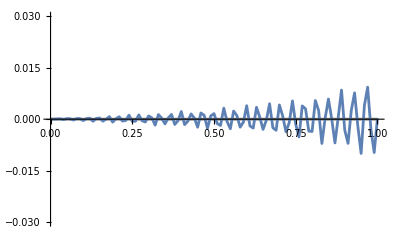

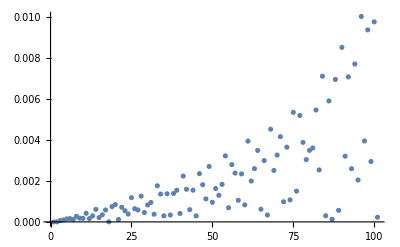

0.0021126

```mathematica
reset[]

updateFunctionCrankNicholson[25/Δt,Q];
plotFunction[{-0.03,0.03}]
plotError[]
Print[error[]];
```